```mathematica
AlphaMin=0.10;
AlphaMax=0.49;
AlphaInterval=0.01;
gfacMin=1.;
gfacMax=1.;
gfacInterval=1.;
nbasMin=8;
nbasMax=10;
nbasInterval=2;
noccMin=1;
noccMax=1;
noccInterval=1;
omegaMin=10;
omegaMax=19;
omegaInterval=1;
c0=1.0;
c1=0.5;
Table[
Table[
Table[
Table[
Table[
res[gfac][nbas][nocc][omega][alpha][c0][c1]= ReadList["/home/grining/drake-mpfun/python/results/nocc="<>ToString[nocc]<>"nbas="<>ToString[nbas]<>"omega="<>ToString[omega]<>"gfac="<>ToString[NumberForm[gfac, {2,2}]]<>"alpha="<>ToString[NumberForm[alpha, {2,2}]]<>"c0="<>ToString[NumberForm[c0, {2,2}]]<>"c1="<>ToString[NumberForm[c1, {2,2}]]<>".out_FCCD"][[1]]
,{gfac, gfacMin, gfacMax,gfacInterval}];
,{nbas, nbasMin,nbasMax,nbasInterval}];
,{nocc, noccMin,noccMax,noccInterval}];
,{omega,omegaMin, omegaMax, omegaInterval}];
,{alpha,AlphaMin,AlphaMax,AlphaInterval}];
```

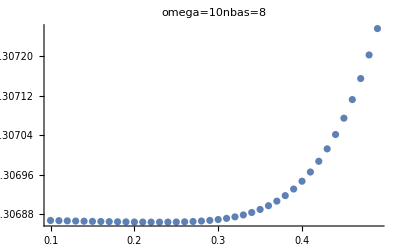
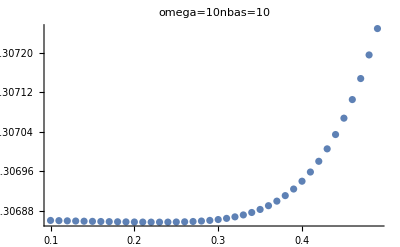
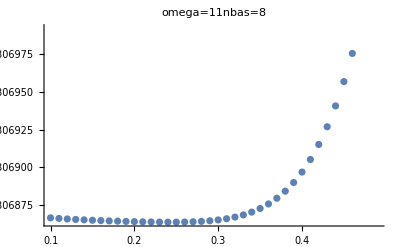
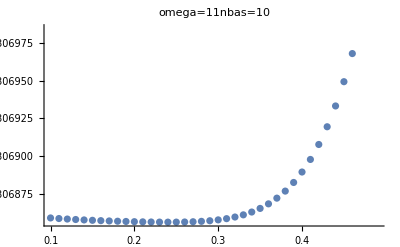
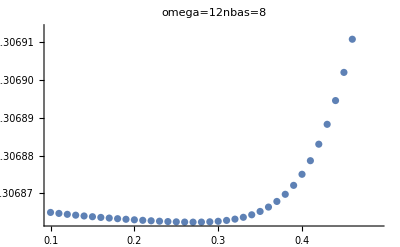
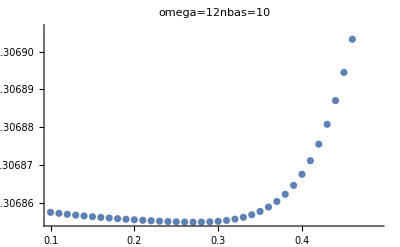
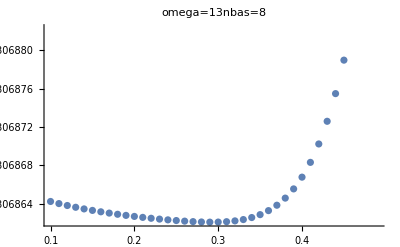
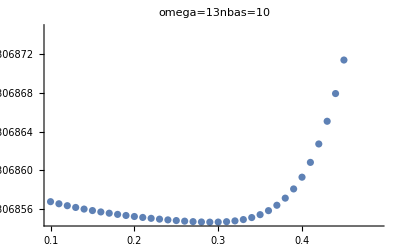

```mathematica
Table[
Res[omega]=Table[
{alpha, res[1.][nbas][1][omega][alpha][1.00][0.50]},
 {alpha,AlphaMin,AlphaMax,AlphaInterval}
];
ListPlot[Res[omega],ImageSize->400, PlotLabel->"omega="<>ToString[omega]<>"nbas="<>ToString[nbas]],
{omega,omegaMin, omegaMax, omegaInterval},{nbas, nbasMin,nbasMax,nbasInterval}
]
```